## Modelo de Drude

## En términos de hω

```mathematica
c=3*^17; (*nm s^-1*)
ℏ=6.582119569*10^(-16); (*eV s*)
```

```mathematica
ϵℏω[ℏω_,ℏωp_,ℏγ_]:=1-((ℏωp/ℏ)^2/((ℏω/ℏ)((ℏω/ℏ)+ I * (ℏγ/ℏ))))(*recibe en eV*)
```

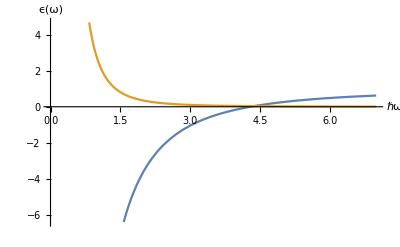

```mathematica
Plot[{Re[ϵℏω[ℏω,4.3,0.15]],Im[ϵℏω[ℏω,4.3,0.15]]},{ℏω,0,7},AxesLabel->{"ℏω","ϵ(ω)"}]
```

```mathematica
Nindexϵℏω[ℏω_,ℏωp_,ℏγ_]:=Sqrt[ϵℏω[ℏω,ℏωp,ℏγ]]
```

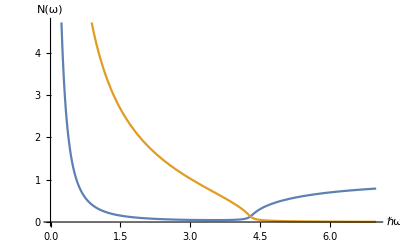

```mathematica
Plot[{Re[Nindexϵℏω[ℏω,4.3,0.15]],Im[Nindexϵℏω[ℏω,4.3,0.15]]},{ℏω,0,7},AxesLabel->{"ℏω","N(ω)"}]
```

## En términos de ω

```mathematica
ϵω[ω_,ωp_,γ_]:=1-(ωp^2/(ω(ω+ ⅈ  γ)))(*recibe en unidades en SI*)
```

```mathematica
ωp1=4.3/ℏ;
γ1=(0.15/ℏ);
```

```mathematica
Plot[{Re[ϵω[ω,ωp1,γ1]],Im[ϵω[ω,ωp1,γ1]]},{ω,0,10*10^(15)},AxesLabel->{"ω","ϵ(ω)"}]
```

-Graphics-

```mathematica
Nindexϵω[ω_,ωp_,γ_]:=Sqrt[ϵ[ω,ωp1,γ1]]
```

```mathematica
Plot[{Re[Nindexϵω[ω,ωp1,γ1]],Im[Nindexϵω[ω,ωp1,γ1]]},{ω,0,9*10^(15)},AxesLabel->{"ω","N(ω)"}]
```

-Graphics-

## En términos de λ

```mathematica
ϵλ[λ_,λp_,γ_]:=1-((2 Pi c/λp)^2/((2 Pi c/λ)((2 Pi c/λ)+ I γ)))(*recibe λ en nm*)
```

```mathematica
λp1=2 Pi c/(4.3/ℏ);
```

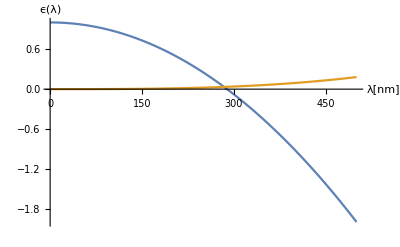

```mathematica
Plot[{Re[ϵλ[λ,λp1,γ1]],Im[ϵλ[λ,λp1,γ1]]},{λ,0,500},AxesLabel->{"λ[nm]","ϵ(λ)"}]
```

```mathematica
Nindexϵλ[λ_,λp_,γ_]:=Sqrt[ϵλ[λ,λp,γ]]
```

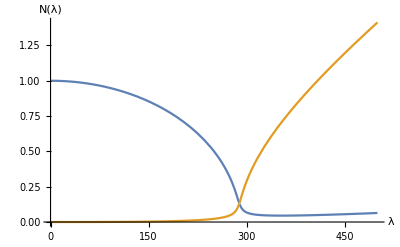

```mathematica
Plot[{Re[Nindexϵλ[λ,λp1,γ1]],Im[Nindexϵλ[λ,λp1,γ1]]},{λ,0,500},AxesLabel->{"λ","N(λ)"}]
```

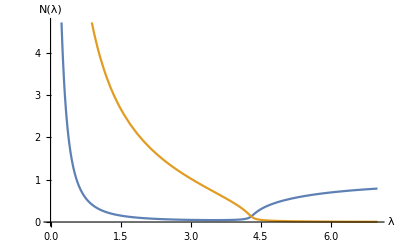

```mathematica
Plot[{Re[Nindexϵλ[h c/λ,λp1,γ1]],Im[Nindexϵλ[h c/λ,λp1,γ1]]},{λ,0,7},AxesLabel->{"λ","N(λ)"}]
```

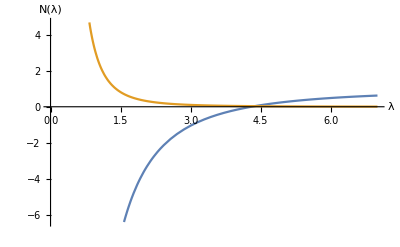

```mathematica
Plot[{Re[ϵλ[h c/λ,λp1,γ1]],Im[ϵλ[h c/λ,λp1,γ1]]},{λ,0,7},AxesLabel->{"λ","N(λ)"}]
```